## Color Space Conversions

```mathematica
rgb2xyz:=Function[rgb,100{{0.4124,0.3576,0.1805},{0.2126,0.7152,0.0722},{0.0193,0.1192,0.9505}}.Map[(If[#>0.04045,((#+0.055)/1.055)^2.4,#/12.92])&,rgb]]
```

```mathematica
xyz2rgb:=Function[xyz,Map[(If[#>0.0031308,1.055(#^(1/2.4))-0.055,12.92#])&,(1/100){{3.2406254773200533,-1.5372079722103187,-0.49862859869824777},{-0.9689307147293197,1.8757560608852415,0.04151752384295395},{0.05571012044551063,-0.20402105059848671,1.0569959422543882}}.xyz]]
```

```mathematica
xyz2lab:=Function[xyz,{{0,116,0,-16},{500,-500,0,0},{0,200,-200,0}}.Append[Map[(If[#>0.008856,#^(1/3),7.787#+16/116])&,xyz/{95.047,100,108.883}],1]]
```

```mathematica
lab2xyz:=Function[lab,Map[(If[#^3>0.008856,#^3,(#-16/116)/7.787])&,({{1/116,1/500,0,16/116},{1/116,0,0,16/116},{1/116,0,-1/200,16/116}}.Append[lab,1])⟦{1,2,3}⟧]{95.047,100,108.883}]
```

```mathematica
rgb2lab=Composition[xyz2lab,rgb2xyz];
```

```mathematica
lab2rgb=Composition[xyz2rgb,lab2xyz];
```

```mathematica
lab2msh:=Function[lab,{Sqrt[l^2+a^2+b^2],ArcCos[l/Sqrt[l^2+a^2+b^2]],If[(a≠0)&&(b≠0),ArcTan[a,b],0]}/.{l->lab⟦1⟧,a->lab⟦2⟧,b->lab⟦3⟧}]
```

```mathematica
msh2lab:=Function[msh,{M Cos[s],M Sin[s]Cos[h],M Sin[s]Sin[h]}/.{M->msh⟦1⟧,s->msh⟦2⟧,h->msh⟦3⟧}]
```

### Approximations that are have errors when values in the triples are small.

```mathematica
rgb2xyzApprox:=Function[rgb,100{{0.4124,0.3576,0.1805},{0.2126,0.7152,0.0722},{0.0193,0.1192,0.9505}}.(((rgb+0.055)/1.055)^2.4)]
```

```mathematica
xyz2rgbApprox:=Function[xyz,Abs[1.055(((1/100){{3.2406254773200533,-1.5372079722103187,-0.49862859869824777},{-0.9689307147293197,1.8757560608852415,0.04151752384295395},{0.05571012044551063,-0.20402105059848671,1.0569959422543882}}.xyz)^(1/2.4))-0.055]]
```

```mathematica
xyz2labApprox:=Function[xyz,{{0,116,0,-16},{500,-500,0,0},{0,200,-200,0}}.Append[(xyz/{95.047,100,108.883})^(1/3),1]]
```

```mathematica
lab2xyzApprox:=Function[lab,((({{1/116,1/500,0,16/116},{1/116,0,0,16/116},{1/116,0,-1/200,16/116}}.Append[lab,1])⟦{1,2,3}⟧)^3){95.047,100,108.883}]
```

## Determine if a particular color is representable on a standard rgb display.

```mathematica
rgbvalid:=Function[rgb,((r≥0)&&(r≤1)&&(g≥0)&&(g≤1)&&(b≥0)&&(b≤1))/.{r->rgb⟦1⟧,g->rgb⟦2⟧,b->rgb⟦3⟧}]
```

```mathematica
xyzvalid:=Function[xyz,rgbvalid[xyz2rgb[xyz]]]
```

```mathematica
labvalid:=Function[lab,xyzvalid[lab2xyz[lab]]]
```

```mathematica
xyzvalidApprox:=Function[xyz,rgbvalid[xyz2rgbApprox[xyz]]]
```

```mathematica
labvalidApprox:=Function[lab,xyzvalidApprox[lab2xyzApprox[lab]]]
```

### Given a particular a and b, what is the maximum L you can achieve on a typical display?

```mathematica
maxL:=Function[{a,b},NMaximize[{L,labvalid[{L,a,b}]},{L}]⟦1⟧]
```

```mathematica
maxL[50,0]
```

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {-1 + If[« 1 »] ≤ 0, -« 1 » ≤ 0, « 2 », -1 + If[1/100\ (-208.013\ If[« 3 »] + 308.012\ If[« 3 »]) > 0.0031308, 1.055\ « 1 » - « 6 », « 1 »] ≤ 0, -« 1 » ≤ 0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

70.4839

```mathematica
maxLApprox:=Function[{a,b},NMaximize[{L,labvalidApprox[{L,a,b}]},{L}]⟦1⟧]
```

```mathematica
maxLApprox[50,0]
```

70.4839

## Brewer

```mathematica
brewer=Reverse[{{178,24,43},{214,96,77},{244,165,130},{253,219,199},{247,247,247},{209,229,240},{146,197,222},{67,147,195},{33,102,172}}/255]
```

{{11/85,2/5,172/255},{67/255,49/85,13/17},{146/255,197/255,74/85},{209/255,229/255,16/17},{247/255,247/255,247/255},{253/255,73/85,199/255},{244/255,11/17,26/51},{214/255,32/85,77/255},{178/255,8/85,43/255}}

```mathematica
xyz2lab[rgb2xyz[{247/255,247/255,247/255}]]
```

{97.2321,0.00513498,-0.0101598}

```mathematica
maxL[0.0051349780675309376,-0.010159832655517675]
```

maxL[0.00513498,-0.0101598]

```mathematica
Map[({xyz2lab[rgb2xyz[#]]⟦1⟧,xyz2lab[rgb2xyz[#]]⟦2⟧})&,brewer]
```

{{42.4674,4.43926},{58.0379,-9.37333},{76.8709,-10.5929},{89.806,-4.43676},{97.2321,0.00513498},{89.7055,8.75681},{74.6702,25.3124},{55.2754,45.0994},{38.3626,58.6602}}

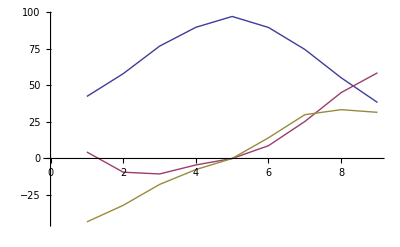

```mathematica
ListPlot[{(xyz2lab[rgb2xyz[#1]]⟦1⟧&)/@brewer,(xyz2lab[rgb2xyz[#1]]⟦2⟧&)/@brewer,(xyz2lab[rgb2xyz[#1]]⟦3⟧&)/@brewer,(maxL[xyz2lab[rgb2xyz[#1]]⟦2⟧,xyz2lab[rgb2xyz[#1]]⟦3⟧]&)/@brewer},Joined->True]
```

## Finding a hue spin

Ideally, we would use the Msh space to hold M and h constant and then swing s from some value to 0.  However, the swing causes the vector to leave the gamut of displayable colors unless M is lowered to the point where the colors are no longer vibrant.  To counter this, we will also linearly change M.  One consequence of this is that the colors change more "quickly" when M is larger.  We can largely correct this problem by also changing hue.  The hue will cause a bigger change when there is more saturation (and where we are defining M to be smaller).  This section determines a good value for the ending h given a starting M, s, and h and an ending M (with the ending s assumed to be 0).  The function is defined in the range 0-1/2, since it will cover half of the domain of a full divergent color map.

```mathematica
cmsh={2(M2-M1)x+M1,(1-2x)s1,2(h2-h1)x+h1}
```

{M1+2 (-M1+M2) x,s1 (1-2 x),h1+2 (-h1+h2) x}

```mathematica
clab=msh2lab[cmsh]
```

{(M1+2 (-M1+M2) x) Cos[s1 (1-2 x)],(M1+2 (-M1+M2) x) Cos[h1+2 (-h1+h2) x] Sin[s1 (1-2 x)],(M1+2 (-M1+M2) x) Sin[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x]}

The perceptual rate of change of a color map (with respect to changes in the scalar value) is given by the magnitude of the piecewise derivative of the function in CIELAB space.  (I show this in my lab journal on 8/7/2007.)  The following resolves this perceptual rate of change given the linearly changing M, s, and h values defined above.

```mathematica
Map[Function[color,(Derivative[1][(Evaluate[color/.x->#])&])[x]],clab]
```

{2 (-M1+M2) Cos[s1 (1-2 x)]+2 s1 (M1+2 (-M1+M2) x) Sin[s1 (1-2 x)],-2 s1 (M1+2 (-M1+M2) x) Cos[s1 (1-2 x)] Cos[h1+2 (-h1+h2) x]+2 (-M1+M2) Cos[h1+2 (-h1+h2) x] Sin[s1 (1-2 x)]-2 (-h1+h2) (M1+2 (-M1+M2) x) Sin[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x],2 (-h1+h2) (M1+2 (-M1+M2) x) Cos[h1+2 (-h1+h2) x] Sin[s1 (1-2 x)]-2 s1 (M1+2 (-M1+M2) x) Cos[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x]+2 (-M1+M2) Sin[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x]}

```mathematica
Sqrt[%.%]
```

√((2 (-M1+M2) Cos[s1 (1-2 x)]+2 s1 (M1+2 (-M1+M2) x) Sin[s1 (1-2 x)])^2+(2 (-h1+h2) (M1+2 (-M1+M2) x) Cos[h1+2 (-h1+h2) x] Sin[s1 (1-2 x)]-2 s1 (M1+2 (-M1+M2) x) Cos[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x]+2 (-M1+M2) Sin[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x])^2+(-2 s1 (M1+2 (-M1+M2) x) Cos[s1 (1-2 x)] Cos[h1+2 (-h1+h2) x]+2 (-M1+M2) Cos[h1+2 (-h1+h2) x] Sin[s1 (1-2 x)]-2 (-h1+h2) (M1+2 (-M1+M2) x) Sin[s1 (1-2 x)] Sin[h1+2 (-h1+h2) x])^2)

```mathematica
FullSimplify[%]
```

√2 √(2 M1^2+h1^2 M1^2-2 h1 h2 M1^2+h2^2 M1^2-4 M1 M2+2 M2^2+2 M1^2 s1^2-4 M1 (M1-M2) ((h1-h2)^2+2 s1^2) x+4 (M1-M2)^2 ((h1-h2)^2+2 s1^2) x^2-(h1-h2)^2 (M1-2 M1 x+2 M2 x)^2 Cos[s1 (2-4 x)])

```mathematica
cdmag=%;
```

We want the perceptual rate of change to be constant.  That is not really possible, but we can get mighty close by adjusting h2 such that the rate of change is equal at the doman extrema (x = 0 and x = 1/2).  At x = 1/2, the hue values should drop out of the equation because a change in hue has no effect when saturation is 0.

```mathematica
cdmag/.x->1/2
```

√2 √(2 M1^2+h1^2 M1^2-2 h1 h2 M1^2+h2^2 M1^2-4 M1 M2+2 M2^2-(h1-h2)^2 M2^2+2 M1^2 s1^2-2 M1 (M1-M2) ((h1-h2)^2+2 s1^2)+(M1-M2)^2 ((h1-h2)^2+2 s1^2))

```mathematica
FullSimplify[%]
```

2 √((M1-M2)^2+M2^2 s1^2)

Now that we know the perceptual rate of change at x = 1/2, find it at x = 0 and build an equation with it.  Then solve.

```mathematica
FullSimplify[%==cdmag/.x->0]
```

2 (-M1^2+M2^2) s1^2+(h1-h2)^2 M1^2 Cos[2 s1]==(h1-h2)^2 M1^2

```mathematica
Solve[%,h2]
```

{{h2→(-h1 M1^2+h1 M1^2 Cos[2 s1]-√2 √(-M1^4 s1^2+M1^2 M2^2 s1^2+M1^4 s1^2 Cos[2 s1]-M1^2 M2^2 s1^2 Cos[2 s1]))/(-M1^2+M1^2 Cos[2 s1])},{h2→(-h1 M1^2+h1 M1^2 Cos[2 s1]+√2 √(-M1^4 s1^2+M1^2 M2^2 s1^2+M1^4 s1^2 Cos[2 s1]-M1^2 M2^2 s1^2 Cos[2 s1]))/(-M1^2+M1^2 Cos[2 s1])}}

```mathematica
FullSimplify[%]
```

{{h2→h1+(Csc[s1]^2 √(M1^2 (-M1^2+M2^2) s1^2 Sin[s1]^2))/M1^2},{h2→h1-(Csc[s1]^2 √(M1^2 (-M1^2+M2^2) s1^2 Sin[s1]^2))/M1^2}}

Mathematica is being conservative here.  If we use some of our domain knowledge, we can resolve h2 to be h1 +/- the following

```mathematica
s1 Sqrt[M2^2-M1^2]/(Sin[s1]M1)
```

(√(-M1^2+M2^2) s1 Csc[s1])/M1